```mathematica
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching "Global`*".

Remove::rmnsm: There are no symbols matching ""Global`*"". ButtonBox["»", Appearance->{Automatic, None}, BaseStyle->"Link", ButtonData:>"paclet:ref/message/Remove/rmnsm", ButtonNote->"Remove::rmnsm"]

```mathematica
SetDirectory["~/work/kago/data/CAP/L2/DEGAUSSED/1/degaussed"]
```

/home/andrew/work/kago/data/CAP/L2/DEGAUSSED/1/degaussed

```mathematica
dat=Import["AllSpins.txt","Table"];
```

```mathematica
originGS=Import["gs.txt","Table"];
```

```mathematica
nspins=(Length[dat])/4
spins=Table[{0,0,0},{i,1,nspins}];
```

27

```mathematica
Do[spins[[i,1]]=dat[[4i-2]];
spins[[i,2]]=dat[[4i-1]];
spins[[i,3]]=dat[[4i]],{i,1,nspins}]
```

Check (the last) spin configuration against the file.

```mathematica
spins[[1]]//MatrixForm
```

(0.712515 | 0.596865 | -0.368882
-0.0208126 | 0.701348 | -0.712515
-0.701348 | 0.389695 | -0.596865)

Check the Byron relationship

```mathematica
tol=10^-6;
Do[Print["config",i-1," check a ",If[spins[[i,1,1]]+spins[[i,2,3]]<tol,0,"oops"], 
" check e ",
If[ spins[[i,2,2]]+spins[[i,3,1]]<tol,0,"oops"],
" check d ",
If[spins[[i,2,1]]+spins[[i,1,3]]+spins[[i,3,2]]<(tol),0,"oops"]],{i,1,nspins}];
```

config0 check a 0 check e 0 check d 0

config1 check a 0 check e 0 check d 0

config2 check a 0 check e 0 check d 0

config3 check a 0 check e 0 check d 0

config4 check a 0 check e 0 check d 0

config5 check a 0 check e 0 check d 0

config6 check a 0 check e 0 check d 0

config7 check a 0 check e 0 check d 0

config8 check a 0 check e 0 check d 0

config9 check a 0 check e 0 check d 0

config10 check a 0 check e 0 check d 0

config11 check a 0 check e 0 check d 0

config12 check a 0 check e 0 check d 0

config13 check a 0 check e 0 check d 0

config14 check a 0 check e 0 check d 0

config15 check a 0 check e 0 check d 0

config16 check a 0 check e 0 check d 0

config17 check a 0 check e 0 check d 0

config18 check a 0 check e 0 check d 0

config19 check a 0 check e 0 check d 0

config20 check a 0 check e 0 check d 0

config21 check a 0 check e 0 check d 0

config22 check a 0 check e 0 check d 0

config23 check a 0 check e 0 check d 0

config24 check a 0 check e 0 check d 0

config25 check a 0 check e 0 check d 0

config26 check a 0 check e 0 check d 0

Now let’s take a look at what θ and ϕ values Andrew’s configurations correspond to.

tan ϕ = b/a (= sinθ sinϕ / sinθ cosϕ = y/x)
ArcTan[x,y]
cosθ=c

```mathematica
theta=Table[0,{i,1,nspins}];
phi=Table[0,{i,1,nspins}];
Do[theta[[i]]=ArcCos[spins[[i,1,3]]];
phi[[i]]=ArcTan[spins[[i,1,1]],spins[[i,1,2]]],{i,1,nspins}]
```

```mathematica
Do[If[theta[[i]]≤π/2,tmp=2*(π/2-theta[[i]]);th0=theta[[i]];theta[[i]]=th0+tmp,],{i,1,nspins,1}]
```

```mathematica
Do[If[phi[[i]]>π/4,tmp=2*(π/4-phi[[i]]);ph0=phi[[i]];phi[[i]]=ph0+tmp,],{i,1,nspins,1}]
```

```mathematica
Bound[ϕ_]:=If[Cos[4 ϕ]==1,π/3,ArcSin[√((4-√(16-6(1-Cos[4 ϕ])))/(1-Cos[4ϕ]))]]
```

```mathematica
marker1=Graphics[{RGBColor[0.22,0.6,0.32],Disk[]}];
marker2=Graphics[{RGBColor[0.13,0.83,1],Disk[]}];
```

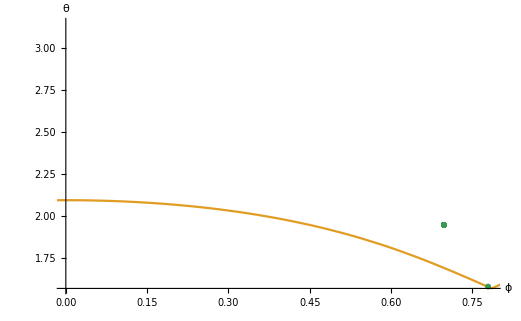

```mathematica
gsPlot=ListPlot[originGS,PlotStyle->Orange];
confPlot=ListPlot[Transpose[{phi,theta}],Frame->{True,True,False,False},FrameLabel->{"ϕ","θ"},Axes->False,PlotRangePadding->Automatic,PlotMarkers->{marker1,0.015}];
boundPlot=Plot[{Bound[ϕ],π-Bound[ϕ]},{ϕ,-π,π},PlotRange->{{0,π/4},{π/2,π}},AxesLabel->{"ϕ","θ"}];
Show[{boundPlot,confPlot},FrameLabel->{"ϕ","θ"}]
```

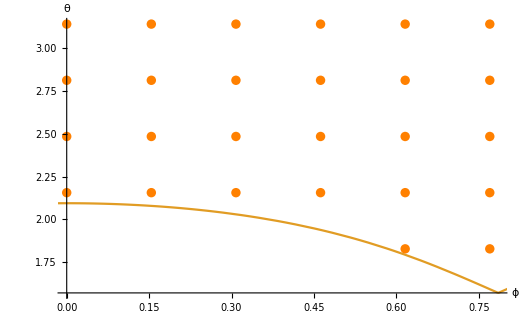

```mathematica
Show[{boundPlot,gsPlot},FrameLabel->{"ϕ","θ"}]
```

```mathematica
-0.254258246482
```

-0.254258

```mathematica
theta//MatrixForm
```

(1.9486
1.9486
1.9486
1.9486
1.9486
1.9486
1.9486
1.9486
1.9486
1.9486
1.58175
1.9486
1.9486
1.9486
1.9486
1.9486
1.9486
1.9486
1.9486
1.58175
1.9486
1.9486
1.9486
1.9486
1.9486
1.9486
1.9486)

```mathematica
phi//MatrixForm
```

(0.697303
0.697303
0.697303
0.697303
0.697303
0.697303
0.697303
0.697303
0.697303
0.697303
0.778825
0.697303
0.697303
0.697303
0.697303
0.697303
0.697303
0.697303
0.697303
0.778825
0.697303
0.697303
0.697303
0.697303
0.697303
0.697303
0.697303)

```mathematica
animation=Manipulate[Show[boundPlot,ListPlot[{{phi[[i]],theta[[i]]}}],ListPlot[{{Hangles[[i,1]],Hangles[[i,2]]}},PlotStyle->{Red}],ImageSize->{700,500}],{i,1,nspins,1},ContentSize->{700,500},AutorunSequencing->{{10,10}}]
```

Part::partd: Part specification Hangles⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification Hangles⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification Hangles⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification Hangles⟦1,2⟧ is longer than depth of object.